## Base model - analytic

```mathematica
Lambda[rh_,mh_,re_,me_]:=1/2 (re+rh-me-mh+√((-re-rh+me+mh)^2-4 (re rh-re me-rh mh)))
```

```mathematica
Lambdaratio[Rr_,m_]:=Lambda[Rr,m,1,m]
```

```mathematica
DLambdaDrho[rho_,m_]:=1/2 (1+(-1+rho)/(√((-1+rho)^2+4 m^2)))
```

```mathematica
DLambdaDt[rho_,m_]:=-1+(2 m)/(√((-1+rho)^2+4 m^2))
```

```mathematica
Solve[DLambdaDrho[rho,m]==-DLambdaDt[rho,m],m]
```

{{m→0},{m→-2/3 (-1+rho)}}

## Competition in the host compartment

```mathematica
eq1={D[nH[t],t]==rh*nH[t]-me*nH[t]+mh*nE[t]-Kh*(nH[t])^2,nH[0]==nH0}
```

{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-Kh nH[t]^2,nH[0]==nH0}

```mathematica
eq2={D[nE[t],t]==me*nH[t]+(re-mh)nE[t],nE[0]==nE0}
```

{nE'[t]==(-mh+re) nE[t]+me nH[t],nE[0]==nE0}

```mathematica
sys={eq1,eq2}
```

{{nH'[t]==mh nE[t]-me nH[t]+rh nH[t]-Kh nH[t]^2,nH[0]==nH0},{nE'[t]==(-mh+re) nE[t]+me nH[t],nE[0]==nE0}}

```mathematica
Biglambda[tmax_,nh0_,ne0_,nhf_,nef_]:=(1/tmax)*Log[(nhf+nef)/(nh0+ne0)];
```

### Equilibrium

```mathematica
eq1U=0==rE*nE-mH*nE+mE*nH
```

0==-mH nE+mE nH+nE rE

```mathematica
eq2U=0==rH*nH-mE*nH+mH*nE-k*nH*nH
```

0==mH nE-mE nH-k nH^2+nH rH

```mathematica
sysU={eq1U,eq2U}
```

{0==-mH nE+mE nH+nE rE,0==mH nE-mE nH-k nH^2+nH rH}

```mathematica
SolU=FullSimplify[Solve[sysU/.mE->m/.mH->m/.rE->1/.rH->rho,{nE,nH}]]
```

{{nE→0,nH→0},{nE→(m (m+(-1+m) rho))/(k (-1+m)^2),nH→(m+(-1+m) rho)/(k (-1+m))}}

```mathematica
(*Diverges in m=1, is positive only for m>1*)
```

```mathematica
nEU[rho_,m_]:=(m (m+(-1+m) rho))/(k (-1+m)^2)
```

```mathematica
nHU[rho_,m_]:=(m/(-1+m)+rho)/k
```

```mathematica
(*It is easy to look at the sign of those equilibria analytically (and also to calculate them). First of all, we have nEU=-(m/(1-m))nHU. Which means, since we only consider positive m, that if we want both of them to be positive at the same time then we need n>1. Then we can look at the positivity of just nHU. Since k is positive we find that nHU is positive if m+rho(m-1)>0 ie m>rho/(1+rho). Let us look at  *)
```

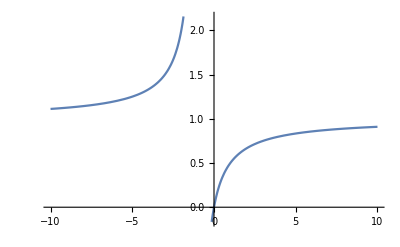
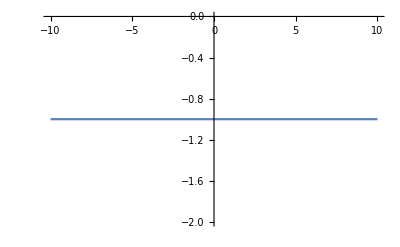
Sho[-Graphics-,-Graphics-]

```mathematica
Sho[Plot[rho/(1+rho),{rho,-10,10}],Plot[-1,{rho,-10,10}]]
```

```mathematica
(*For the region of the parameter space we are interested in (rho>-1) the condition m>1 is thus sufficient for the existence of a positive equilibrium. Intuitively it makes sense: if migration is so important that microbes migrate out of the environment faster than they replicate in it (m>rE) then the exponential growth never truly has the time to kick in and competition is efficient everywhere despite formally existing only in the host. If migration is smaller than replication though, we DO have dnE/dt always positive, and a population that explodes in the environment.*)
```

### Sensitivity of the equilibrium population sizes

```mathematica
finalPop[rho_,m_]:=nEU[rho,m]+nHU[rho,m]
```

```mathematica
FullSimplify[D[finalPop[rho,m],rho]]
```

(2+1/(-1+m))/k

```mathematica
DLDRHO[rho_,m_]:=(2+1/(-1+m))/k
```

```mathematica
FullSimplify[D[finalPop[rho,m],m]]
```

(1+rho-m (3+rho))/(k (-1+m)^3)

```mathematica
DLDM[rho_,m_]:=(1+rho-m (3+rho))/(k (-1+m)^3)
```

```mathematica
Sol=Refine[Solve[DLDM[rho,m]==-DLDRHO[rho,m],m],m>0&&rho<1&&rho>-1]
```

{{m→5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3)},{m→5/6+((1+ⅈ √3) (-19-6 rho))/(12 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))-1/12 (1-ⅈ √3) (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3)},{m→5/6+((1-ⅈ √3) (-19-6 rho))/(12 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))-1/12 (1+ⅈ √3) (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3)}}

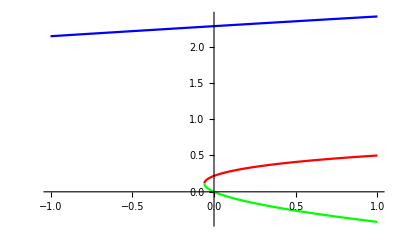

```mathematica
Plot[{m/.Sol[[1]],m/.Sol[[2]],m/.Sol[[3]]},{rho,-1,1},PlotRange->All,PlotStyle->{Blue,Green,Red}]
```

```mathematica
(*The two branches below are out of the zone where an equilibrium exists so can be dismissed*)
```

```mathematica
Sol2=Refine[Solve[DLDM[rho,m]==DLDRHO[rho,m],m],m>0&&rho<1&&rho>-1]
```

{{m→5/6+(17+6 rho)/(6 (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3))-1/6 (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3)},{m→5/6-((1+ⅈ √3) (17+6 rho))/(12 (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3))+1/12 (1-ⅈ √3) (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3)},{m→5/6-((1-ⅈ √3) (17+6 rho))/(12 (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3))+1/12 (1+ⅈ √3) (82-9 rho+3 √3 √(431+138 rho+71 rho^2+8 rho^3))^(1/3)}}

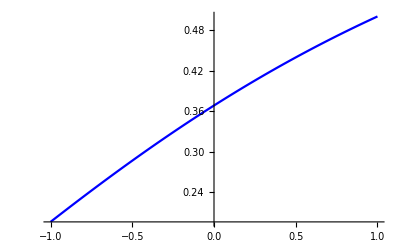

```mathematica
Plot[{m/.Sol2[[1]],m/.Sol2[[2]],m/.Sol2[[3]]},{rho,-1,1},PlotRange->All,PlotStyle->{Blue,Green,Red}]
```

```mathematica
(*Also out of the equilibrium zone*)
```

## Parametric maps of λ - Panel A

### Definition of parameters and discretization of the trait space

```mathematica
tmax = 30;
NE0 =1;
NH0 = 0;
RE = 1;
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Table[i,{i,0,3,0.05}];
TabKH ={10^-12,10^-8,10^-4};
Rempl = Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh-> TabKH⟦ikh⟧},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

### Solution on the primary lattice

```mathematica
Sol = Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.Rempl⟦irho,im,ikh⟧/.nE0->NE0/.nH0->NH0,{nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
LambdaTab2 = Table[Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ikh⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ikh⟧⟦1⟧⟦1⟧],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ikh,1,Length[TabKH]}];
```

```mathematica
LambdaTab2Array = Reverse[Table[Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ikh⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ikh⟧⟦1⟧⟦1⟧],{im,1,Length[TabM]},{irho,1,Length[TabRHO]},{ikh,1,Length[TabKH]}]];
```

```mathematica
data = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTab2[[irho,im,ikh]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ikh,1,Length[TabKH]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.0001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->TabKH[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->TabKH[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[TabKH]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0/.nH0->NH0,{nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
DMSolGC = Table[{nE[tmax],nH[tmax]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0/.nH0->NH0,{nE,nH},{t,0,tmax}],{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO =Table[(Biglambda[tmax, NH0,NE0,DRHOSolGC⟦irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ik⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
SensiM = Table[(Biglambda[tmax, NH0,NE0,DMSolGC⟦irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmax, NH0,NE0,Sol⟦irho,im,ik⟧⟦1⟧⟦2⟧,Sol⟦irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiRHO = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[irho]][[im]][[ik]]/SensiRHO[[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[TabKH]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

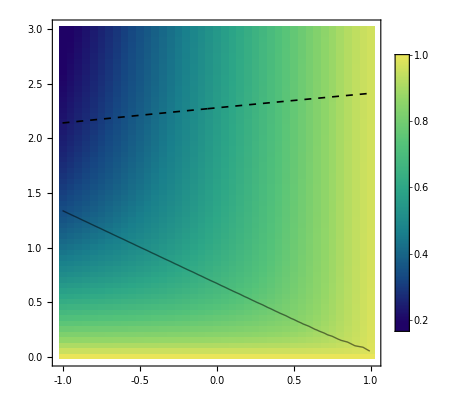
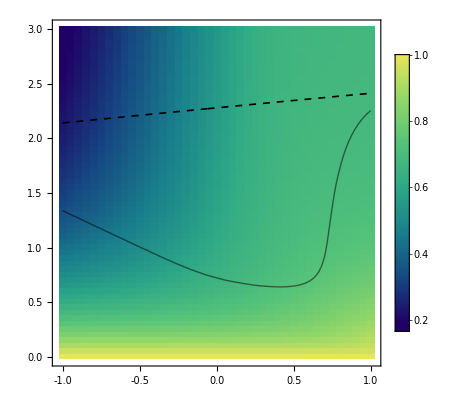
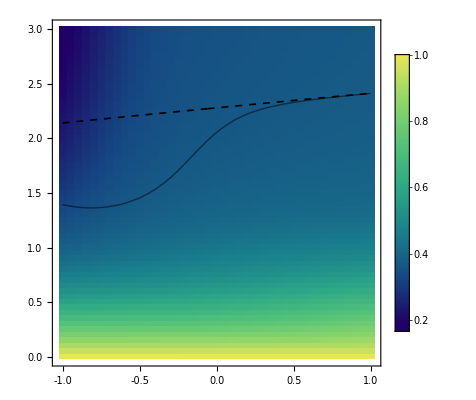

```mathematica
Table[Show[ArrayPlot[LambdaTab2Array[[;;,;;,ikh]],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow"][Rescale[#,{0.19,1}]]&),PlotLegends->Automatic,PlotRange->All,Frame->True,FrameTicks->{{{0,"0.0"},{0.5,"0.5"},{1.0,"1.0"},{1.5,1.5},{2.0,"2.0"},{2.5,2.5},{3.0,"3.0"},{4.0,4.0}},{{-1.0,"-1.0"},{-0.5,-0.5},{0.0,"0.0"},{0.5,0.5},{1.0,"1.0"}},None,None},BaseStyle->{FontSize->16},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold},DataRange->{{-1,1},{0.,3}},AspectRatio->1],ListContourPlot[dataSensiRatio[[ikh]],ContourShading->None,Contours->{1},ContourStyle->Directive[Black,Thick],BaseStyle->{FontSize->16}],ListContourPlot[dataSensiRatio[[ikh]],ContourShading->None,Contours->{-1},ContourStyle->Directive[Black,Thick],BaseStyle->{FontSize->16}],Plot[5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thickness[0.003],Dashed]]],{ikh,1,Length[TabKH]}]
```

## Panel C - Kh=10^-8 fixed, effect of time, nE0 = 0, nH0 = 1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {5,10,20,30,40,50,60,70};
NE0B = 0;
NH0B = 1;
RE = 1;
Listk={10^-8};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =  Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.1,3,0.05}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

NDSolve::ndcf: Repeated convergence test failure at t == 69.1226; unable to continue.

InterpolatingFunction::dmval: Input value {70} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndcf: Repeated convergence test failure at t == 68.8938; unable to continue.

InterpolatingFunction::dmval: Input value {70} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

#### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.0001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO  = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

### Plot

```mathematica
listcolor=Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[tmaxB]-1)}]
```

{RGBColor[0.122103, 0.00901808, 0.39826],RGBColor[0.08943771428571429, 0.24098401142857143, 0.49412457142857147],RGBColor[0.09378314285714286, 0.43570714285714285, 0.5372898571428572],RGBColor[0.14216071428571428, 0.5862125714285714, 0.5369255714285714],RGBColor[0.24151514285714284, 0.699388, 0.505396],RGBColor[0.3987782857142857, 0.7844317142857143, 0.45559771428571433],RGBColor[0.6208947142857143, 0.8482312857142857, 0.39989485714285716],RGBColor[0.914809, 0.897673, 0.350652]}

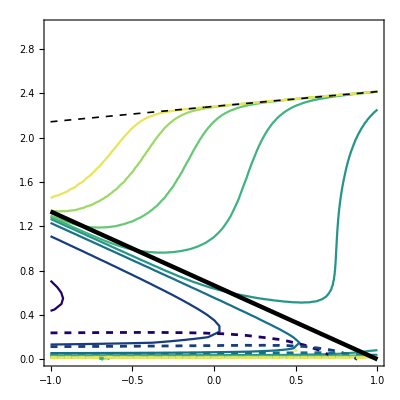

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Opacity[1],Thickness[0.004]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,3}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Opacity[1],Thickness[0.005],Dashed],BaseStyle->{FontSize->16},PlotRange->All],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thickness[0.008]]],Plot[5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thickness[0.003],Dashed]]]
```

## Panel E - tmax=30 fixed, effect of Kh, nE0 = 0, nH0 = 1

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {30};
NE0B = 0;
NH0B = 1;
RE = 1;
Listk=10^-{10,9,8,7,6,5,4,3,2,1};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM = Flatten[{Table[i,{i,0,0.1,0.01}],Table[i,{i,0.15,3,0.05}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

#### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO =  Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

### Plot

```mathematica
listcolor=Table[ColorData["BlueGreenYellow"][k],{k,0,1,1/(Length[Listk]-1)}]
```

{RGBColor[0.122103, 0.00901808, 0.39826],RGBColor[0.09669666666666667, 0.18943602666666667, 0.47282133333333337],RGBColor[0.088562, 0.352474, 0.5227896666666667],RGBColor[0.097699, 0.498132, 0.548165],RGBColor[0.149571, 0.6008926666666666, 0.5350523333333334],RGBColor[0.22684666666666667, 0.688918, 0.5105293333333333],RGBColor[0.329526, 0.762208, 0.474596],RGBColor[0.49111466666666664, 0.8140633333333334, 0.4302666666666667],RGBColor[0.686209, 0.8592183333333334, 0.388952],RGBColor[0.914809, 0.897673, 0.350652]}

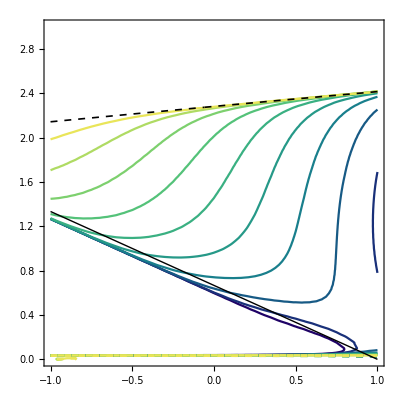

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,ikh]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ikh]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,3}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{ikh,1,Length[Listk]}],Table[ListContourPlot[dataSensiRatio[[1,ikh]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ikh]],Thickness[0.005],Dashed,Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All],{ikh,1,Length[Listk]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thickness[0.003],Dashed]]]
```

## Panel B - nE0 = 1 and nH0 = 0, k=10^-8 fixed, varying time

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {0.1,1,10,30,35,40,45,50,60,70};
NE0B = 1;
NH0B = 0;
RE = 1;
Listk={10^-8};
ALPHA = 1;
TabRHO  = Flatten[{Table[i,{i,-1,0.9,0.05}],Table[i,{i,0.91,1,0.01}]}];
TabM =Flatten[{0,Table[i,{i,0,3,0.05}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataLambda=Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],LambdaTabGC[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.0001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRHO  = dataElasRHO = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiM = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],SensiM[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{ik,1,Length[Listk]},{itmax,1,Length[tmaxB]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

```mathematica
listcolor=Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[tmaxB]-1)}]
```

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6258028888888889, 0.054322222222222216, 0.010549066666666667],RGBColor[0.7828637777777778, 0.10864444444444443, 0.0052745333333333345],RGBColor[0.871407, 0.20684366666666665, 0.013399966666666667],RGBColor[0.937111, 0.3196685555555555, 0.02599205555555556],RGBColor[0.9766378888888889, 0.43626944444444443, 0.04292872222222222],RGBColor[0.9899876666666667, 0.5566463333333334, 0.06420996666666667],RGBColor[1., 0.6661732222222222, 0.08536913333333333],RGBColor[1., 0.7431501111111112, 0.10616206666666668],RGBColor[1., 0.820127, 0.126955]}

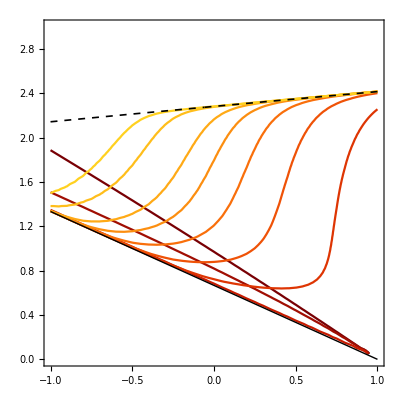

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{0,3}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Table[ListContourPlot[dataSensiRatio[[itmax,1]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[itmax]],Thickness[0.004],Opacity[1],Dashed],BaseStyle->{FontSize->16},PlotRange->All,LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{itmax,1,Length[tmaxB]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thickness[0.003],Dashed]]]
```

## Panel D - nE0 = 1 and nH0 = 0, tmax=20 fixed, varying k

### Definition of parameters and discretization of the trait space

```mathematica
tmaxB = {30};
NE0B = 1;
NH0B = 0;
RE = 1;
Listk=10^-{10,9,8,7,6,5,4,3,2};
ALPHA = 1;
TabRHO  = Table[i,{i,-1,1,0.05}];
TabM =Flatten[{0,0.1,Table[i,{i,0.15,3,0.05}]}];
Rempl = Table[{tmax->tmaxB[[itmax]],re->RE,rh-> RE*TabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the primary lattice

```mathematica
SolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.Rempl⟦itmax,irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
LambdaTabGC = Table[Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Solution on the slightly shifted parameters spaces

```mathematica
α = 0.00001;
```

```mathematica
DTabRHO  = α+TabRHO;
DTabM = α+TabM;
```

```mathematica
DRHORempl = Table[{re->RE,rh-> RE*DTabRHO⟦irho⟧,me-> TabM⟦im⟧,mh->ALPHA*TabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[DTabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
DMRempl=Table[{re->RE,rh-> RE*TabRHO⟦irho⟧,me-> DTabM⟦im⟧,mh->ALPHA*DTabM⟦im⟧,Kh->Listk[[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[DTabM]},{ik,1,Length[Listk]}];
```

```mathematica
DRHOSolGC= Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DRHORempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
DMSolGC = Table[{nE[tmaxB[[itmax]]],nH[tmaxB[[itmax]]]}/.NDSolve[sys/.DMRempl⟦irho,im,ik⟧/.nE0->NE0B/.nH0->NH0B,{nE,nH},{t,0,tmaxB[[itmax]]}],{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

### Calculation of the sensitivities

```mathematica
SensiRHO = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DRHOSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
SensiM = Table[(Biglambda[tmaxB[[itmax]], NH0B,NE0B,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,DMSolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧]-Biglambda[tmaxB[[itmax]], NH0B,NE0B,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦2⟧,SolGC⟦itmax,irho,im,ik⟧⟦1⟧⟦1⟧])/(α),{itmax,1,Length[tmaxB]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]},{ik,1,Length[Listk]}];
```

```mathematica
dataSensiRatio = Table[Flatten[Table[{TabRHO[[irho]],TabM[[im]],-SensiM[[itmax]][[irho]][[im]][[ik]]/SensiRHO[[itmax]][[irho]][[im]][[ik]]},{irho,1,Length[TabRHO]},{im,1,Length[TabM]}],1],{itmax,1,Length[tmaxB]},{ik,1,Length[Listk]}];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

### Plot

```mathematica
listcolor=Table[ColorData["SolarColors"][k],{k,0,1,1/(Length[Listk]-1)}]
```

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6454355, 0.0611125, 0.00988975],RGBColor[0.822129, 0.122225, 0.0039559],RGBColor[0.896046, 0.24915299999999999, 0.018122],RGBColor[0.969963, 0.376081, 0.0322881],RGBColor[0.9849815, 0.511505, 0.0562295],RGBColor[1., 0.646929, 0.0801709],RGBColor[1., 0.733528, 0.10356295000000001],RGBColor[1., 0.820127, 0.126955]}

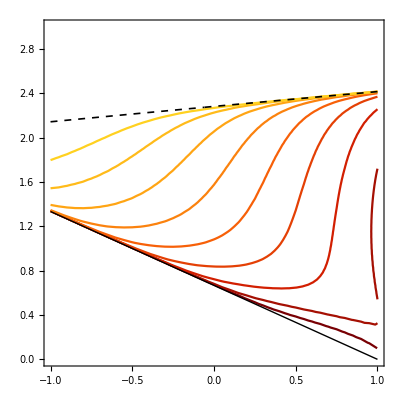

```mathematica
Show[Table[ListContourPlot[dataSensiRatio[[1,ik]],ContourShading->None,Contours->{1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->{{-1,1},{-0.0000001,3}},LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{ik,1,Length[Listk]}],Table[ListContourPlot[dataSensiRatio[[1,ik]],ContourShading->None,Contours->{-1},ContourStyle->Directive[listcolor[[ik]],Thickness[0.004],Opacity[1]],BaseStyle->{FontSize->16},PlotRange->All,LabelStyle->{FontSize->20,FontFamily->"Latin Modern Math",Black,Bold}],{ik,1,Length[Listk]}],Plot[-2/3 (-1+rho),{rho,-1,1},PlotStyle-> Directive[Black,Thick]],Plot[5/6-(-19-6 rho)/(6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3))+1/6 (80-9 rho+3 √3 √(-17-294 rho-73 rho^2-8 rho^3))^(1/3),{rho,-1,1},PlotStyle->Directive[Black,Thickness[0.003],Dashed]]]
```